```mathematica
M1[i,i+c]:=a[i,i+c]
M2[i,i+d]:=b[i,i+d]
(M1^2)[i,i+2c]:=a[i,i+c]*a[i,i+2c]
(M1^n)[i,i+n c]:=∏_(k=1)^n a[i+c(k-1),i+c k]
M1*M2[i,i+c+d]:=a[i,i+c]*b[i+c,i+c+d]
```

```mathematica
a->p
b->c
c->p(i-r)+7q
d->i-r+7
```

```mathematica
∏_(k=0)^(n-1) (a b k +c)/(b k+d)
```

(a^(-1+n) c Pochhammer[1+c/(a b),-1+n])/(d Pochhammer[(b+d)/b,-1+n])

```mathematica
Pochhammer[1+c/(a b),-1+n]=Subscript[(1+c/(a b)), n-1]==Gamma[2+c/(a b)]/Gamma[3+c/(a b)-n]
```

```mathematica
Pochhammer[(b+d)/b,-1+n]==Gamma[2+d/b]/Gamma[3+d/b-n]
```

```mathematica
∏_(k=0)^(n-1) (a b k +c)/(b k+d)==(a^(-1+n) c Pochhammer[1+c/(a b),-1+n])/(d Pochhammer[(b+d)/b,-1+n])==(a^(-1+n) c Gamma[2+c/(a b)]/Gamma[3+c/(a b)-n])/(d Gamma[2+d/b]/Gamma[3+d/b-n])==(a^(-1+n) c Gamma[2+c/(a b)] Gamma[3+d/b-n])/(d Gamma[2+d/b] Gamma[3+c/(a b)-n])
```

```mathematica
(a^(-1+n) c Gamma[2+c/(a b)]/Gamma[3+c/(a b)-n])/(d Gamma[2+d/b]/Gamma[3+d/b-n])
```

(a^(-1+n) c Gamma[2+c/(a b)] Gamma[3+d/b-n])/(d Gamma[2+d/b] Gamma[3+c/(a b)-n])

```mathematica
P[7t+r->7(t+e)+s]:=(p t+q)/(t+u)
m[x,y]:={x=7t+r,y=7(t+e)+s}==(p t+q)/(t+u)
m[i,j]:={i,i+(7e+s-r)}==(p(i-r)+7q)/(i-r+7u)
m[i,i+(7e+s-r)]:=(p(i-r)+7q)/(i-r+7u)
(m^n)[i,i+n(7e+s-r)]:=(p^(-1+n) (p(i-r)+7q) Gamma[2+(p(i-r)+7q)/(p c)] Gamma[3+(i-r+7u)/c-n])/(d Gamma[2+(i-r+7u)/c] Gamma[3+(p(i-r)+7u)/(p c)-n])
```

```mathematica
({{x}, {y}})==Gamma[x+1]/(Gamma[y+1]Gamma[x-y+1])
(x+y)^n==∑_(k=0)^n ({{n}, {k}})x^(n-k)y^k==∑_(k=0)^n Gamma[n+1]/(Gamma[k+1]Gamma[n-k+1])x^(n-k)y^k
```

```mathematica
m1[i,j]+
```

```mathematica
M1[i,i+c]:=a[i,i+c]
M2[i,i+d]:=b[i,i+d]
```

```mathematica
P[7t1+r1->7(t1+e1)+s1]:=(p1 t1+q1)/(t1+u1)
P[7t2+r2->7(t2+e2)+s2]:=(p2 t2+q2)/(t2+u2)
m1[i,j]:={i,i+(7e1+s1-r1)}==(p1(i-r1)+7q1)/(i-r1+7u1)
m2[i,j]:={i,i+(7e2+s2-r2)}==(p2(i-r2)+7q2)/(i-r2+7u2)
(m1^n1)[i,i+n1(7e1+s1-r1)]:=(p1^(-1+n1) (p1(i-r1)+7q1) Gamma[2+(p1(i-r1)+7q1)/(p1 c1)] Gamma[3+(i-r1+7u1)/c1-n1])/(d1 Gamma[2+(i-r1+7u1)/c1] Gamma[3+(p1(i-r1)+7u1)/(p1 c1)-n1])
(m2^n2)[i,i+n2(7e2+s2-r2)]:=(p2^(-1+n2) (p2(i-r2)+7q2) Gamma[2+(p2(i-r2)+7q2)/(p2 c2)] Gamma[3+(i-r2+7u2)/c2-n2])/(d2 Gamma[2+(i-r2+7u2)/c2] Gamma[3+(p2(i-r2)+7u2)/(p2 c2)-n2])
m1^n1*(m2^n2)[i,i+(n1(7e1+s1-r1)+n2(7e2+s2-r2))]:=(p1^(-1+n1) p2^(-1+n2) (7 q1+p1 (i-r1)) (7 q2+p2 (i-r2+n1 (7 e1-r1+s1))) Gamma[2+(7 q1+p1 (i-r1))/(c1 p1)] Gamma[2+(7 q2+p2 (i-r2+n1 (7 e1-r1+s1)))/(c2 p2)] Gamma[3-n1+(i-r1+7 u1)/c1] Gamma[3-n2+(i-r2+n1 (7 e1-r1+s1)+7 u2)/c2])/(d1 d2 Gamma[3-n1+(p1 (i-r1)+7 u1)/(c1 p1)] Gamma[2+(i-r1+7 u1)/c1] Gamma[2+(i-r2+n1 (7 e1-r1+s1)+7 u2)/c2] Gamma[3-n2+(p2 (i-r2+n1 (7 e1-r1+s1))+7 u2)/(c2 p2)])
```

```mathematica
(m1[i,j]+m2[i,j])^n==∑_(k=0)^n (p1^(-1-k+n) p2^(-1+k) (7 q1+p1 (i-r1)) (7 q2+p2 (i-r2+(-k+n) (7 e1-r1+s1))) Gamma[1+n] Gamma[2+(7 q1+p1 (i-r1))/(c1 p1)] Gamma[2+(7 q2+p2 (i-r2+(-k+n) (7 e1-r1+s1)))/(c2 p2)] Gamma[3+k-n+(i-r1+7 u1)/c1] Gamma[3-k+(i-r2+(-k+n) (7 e1-r1+s1)+7 u2)/c2])/(d1 d2 Gamma[1+k] Gamma[1-k+n] Gamma[3+k-n+(p1 (i-r1)+7 u1)/(c1 p1)] Gamma[2+(i-r1+7 u1)/c1] Gamma[2+(i-r2+(-k+n) (7 e1-r1+s1)+7 u2)/c2] Gamma[3-k+(p2 (i-r2+(-k+n) (7 e1-r1+s1))+7 u2)/(c2 p2)])
```

```mathematica
∑_(k=0)^n (p1^(-1-k+n) p2^(-1+k) (7 q1+p1 (i-r1)) (7 q2+p2 (i-r2+(-k+n) (7 e1-r1+s1))) Gamma[1+n] Gamma[2+(7 q1+p1 (i-r1))/(c1 p1)] Gamma[2+(7 q2+p2 (i-r2+(-k+n) (7 e1-r1+s1)))/(c2 p2)] Gamma[3+k-n+(i-r1+7 u1)/c1] Gamma[3-k+(i-r2+(-k+n) (7 e1-r1+s1)+7 u2)/c2])/(d1 d2 Gamma[1+k] Gamma[1-k+n] Gamma[3+k-n+(p1 (i-r1)+7 u1)/(c1 p1)] Gamma[2+(i-r1+7 u1)/c1] Gamma[2+(i-r2+(-k+n) (7 e1-r1+s1)+7 u2)/c2] Gamma[3-k+(p2 (i-r2+(-k+n) (7 e1-r1+s1))+7 u2)/(c2 p2)])
```

$Aborted

```mathematica
Reduce[(m x+b==y||n x+c==y)&&m>0&&x>0&&b>0&&y>0&&n>0&&c>0,Integers]
```

((b|c|m|n|x)∈Integers&&b≥1&&c≥1&&m≥1&&n≥1&&x≥1&&y==b+m x)||((b|c|m|n|x)∈Integers&&b≥1&&c≥1&&m≥1&&n≥1&&x≥1&&y==c+n x)

```mathematica
m[i,j]*v[i]==mv[i]==∑_(j=1) m[i,j]*v[j]
```

```mathematica
m.v=∑_(j=1) m[i,j]*v[j]
m1+m2=m1[i,j]*v[j]+m2[i,j]*v[j]
(∑_(k=1)^n Subscript[m, k]).v==∑_(k=1)^n ∑_(j=1)^∞ Subscript[m, k][i,j]*v[j]
```

```mathematica
(∑_(k=1)^n Subscript[m, k]).v==∑_(k=1)^n ∑_(j=1)^∞ Subscript[m, k][i,7j]*v[7j]
```

```mathematica
∑_(i=1)^∞ (∑_(k=1)^n Subscript[m, k]).v==∑_(i=1)^∞ ∑_(k=1)^n ∑_(j=1)^∞ Subscript[m, k][i,7j]*v[7j]==∑_(k=1)^n (∑_(i=1)^∞ ∑_(j=1)^∞ Subscript[m, k][i,7j]*v[7j])==P["success"]
```

```mathematica
Divisible[6,3]
```

True

```mathematica
Table[Position[Table[Boole[(a+b+c==7m)&&(Divisible[a,7]||Divisible[b,7]||Divisible[c,7])],{a,0,7m},{b,0,7m},{c,0,7m}],1],{m,1,1}]
```

{{{1,1,8},{1,2,7},{1,3,6},{1,4,5},{1,5,4},{1,6,3},{1,7,2},{1,8,1},{2,1,7},{2,7,1},{3,1,6},{3,6,1},{4,1,5},{4,5,1},{5,1,4},{5,4,1},{6,1,3},{6,3,1},{7,1,2},{7,2,1},{8,1,1}}}

```mathematica
Select[Table[Join[Take[Mod[Range[7],7],i],{j}],{i,1,6},{j,1,6}],Mod[Total[#],7]==0&]
```

{}

```mathematica
{Table[Sum[Boole[(a+b+c==7m)],{a,0,7m},{b,0,7m},{c,0,7m}],{m,1,7}],Table[Sum[Boole[(a+b+c==7m)&&(Divisible[a,7]||Divisible[b,7]||Divisible[c,7])],{a,0,7m},{b,0,7m},{c,0,7m}],{m,1,7}]}
```

```mathematica
{{36,120,253,435,666,946,1275},{21,60,118,195,291,406,540}}
```

{{36,120,253,435,666,946,1275},{21,60,118,195,291,406,540}}

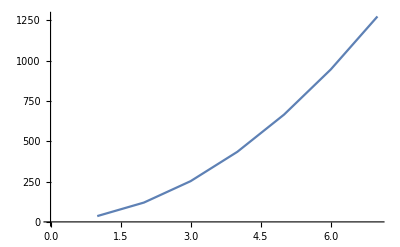
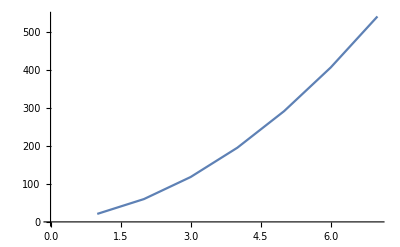

```mathematica
{ListPlot[%[[1]],Joined->True],ListPlot[%[[2]],Joined->True]}
```

```mathematica
ListPlot[{21,60,118,195,291,406,540},Joined->True]
```

-Graphics-

```mathematica
FactorInteger[540]
```

{{2,2},{3,3},{5,1}}